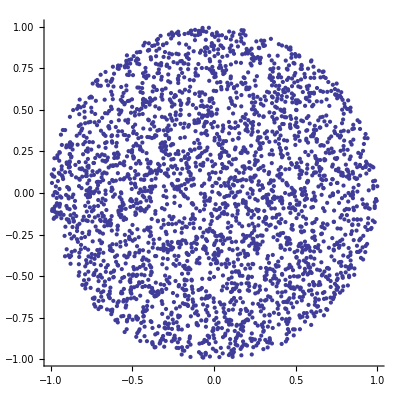

dP/dr=2.95355 r^0.944567

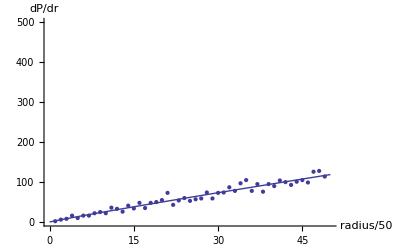

```mathematica
Clear[data];
dim=2;
ptcount=3000;
data=Table[With[{ang=2 π Random[]},(Random[])^(1/dim){Cos[ang],Sin[ang]}],{ptcount}];
ListPlot[data,PlotRange->{{-1,1},{-1,1}},AspectRatio->1,Axes->True]

c=50;
dpdr=Table[Count[data,{x_,y_}/;(i/c)^2≤x^2+y^2≤((i+1)/c)^2],{i,1,c-1}];
Clear[a,H];
model=NonlinearModelFit[dpdr,a*r^H,{a,H},r];
Print["dP/dr=",Normal[model]]

Show[ListPlot[dpdr],Plot[model[u],{u,0,c}],PlotRange->{{0,c},{0,10c}},AxesLabel->{radius/50,dP/dr}]
```

```mathematica
Clear[RanWalkGraphics,RanWalk];

Options[RanWalk]= {StartPoint->Automatic};

RanWalk[data_, eps_, maxn_, opts___]:=
Module[{stpt},
{stpt}={StartPoint}/.{opts}/.Options[RanWalk];
If[stpt===Automatic, stpt = First[RandomSample[data,1]]];
Drop[FixedPointList[Function[{pt},With[{candidates=Select[data, (0.<Norm[#- pt]< eps&)]}, If[candidates==={}, {}, First[RandomSample[candidates,1]]]]], stpt, maxn+1, SameTest->(#2==={}&)],-1]
];

DataGraphicsElements[data_]:=
{ Green, AbsolutePointSize[2], Point/@data};

Options[RanWalkGraphics] = {ShowPoints->True, WalkThickness->1};

RanWalkGraphics[data_, lis_, opts___]:=
Module[{shpt, walkth},
{shpt, walkth}={ShowPoints, WalkThickness}/.{opts}/.Options[RanWalkGraphics];
Graphics[{If[shpt, DataGraphicsElements[data], {}], AbsoluteThickness[walkth], Red,Line[Partition[lis,2,1]], {AbsolutePointSize[6],Black, Point[First[lis]]}, {AbsolutePointSize[6],Blue, Point[Last[lis]]}}]]
```

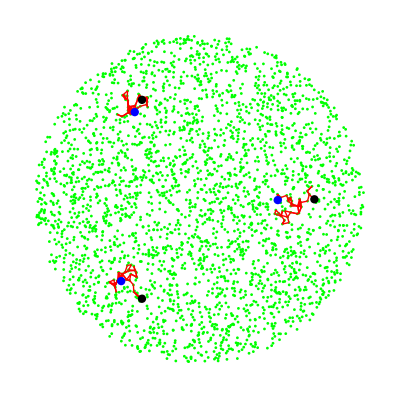

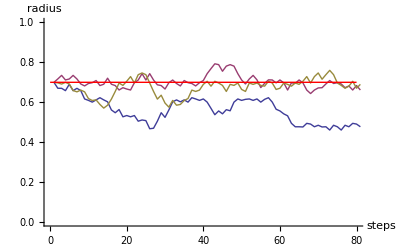

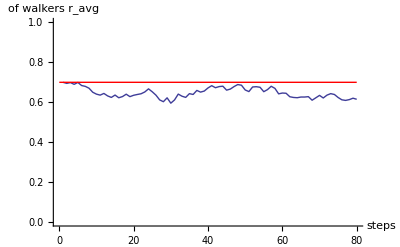

```mathematica
RandomRingWalk[num_, rad_, data_, eps_, maxn_]:=RanWalk[data, eps, maxn, StartPoint -> #]&/@Table[rad{Cos[t],Sin[t]},{t,0,2π(1-1/num), 2π/num}]
num=3;
rad=.7;
eps=.045;
maxn=5Ceiling[rad/eps];
walks = RandomRingWalk[num,rad, data,eps,maxn];
Show[Graphics[DataGraphicsElements[data]],RanWalkGraphics[data, #, ShowPoints->False]&/@walks]

Show[ListPlot[Map[Norm,walks,{2}], Joined->True,PlotRange->{{0,maxn},{0,1}},AxesLabel->{steps,radius}],Plot[rad,{t,0,maxn},PlotStyle->Red]]

sets=Map[Norm,walks,{2}];

all=Flatten[Table[sets[[p]],{p,1,num}]];

ravg=ListPlot[Table[Mean[Table[sets[[i,j]],{i,1,num,1}]],{j,1,maxn,1}],Joined->True,PlotRange->{{0,maxn},{0,1}},AxesLabel->{steps,Subscript[r, avg] of walkers}];
Show[ravg,Plot[rad,{t,0,maxn},PlotStyle->Red]]
```